# Analiza delnic PETG v letu 2018

## Pridobivanje podatkov

Podatke sem pridobil iz spletne strani https://www.ljse.si/ . V navodilu naloge je rečeno naj analiziram delnico PETG za leto 2017, ampak ker
podatkov za to leto nisem našel, sem naredil za leto 2018.

Nastavimo delovni direktorij na direktorij v katerem imam podatke o delnici.

```mathematica
SetDirectory["C:\\Users\\azoma\\Documents\\GitHub\\Projektna-naloga-ROM"];
```

Shranimo podatke. Vemo, da so podatki ločeni z podpičji.

```mathematica
data=Import["data.csv","Table","FieldSeparators"->{";"}];
```

Tukaj si pripravim podatke za kasnejšo obdelavo (risanje na graf, računanje volatilnosti ...). Vsi podatki so narobe urejeni, zato jih obrnem.

```mathematica
datumi = Reverse[DateObject /@ data[[2 ;;, 4]]];
datumiReal = AbsoluteTime /@ datumi;
cene = Reverse[ToExpression /@ StringReplace[data[[2 ;;, 9]], "," -> "."]];
```

Pridobim podatke iz wolframove zbirke podatkov za eurostock in sp500.

```mathematica
sp500=FinancialData["^GSPC",{{2018,1,1},{2018,12,31},"Day"}];
dax=FinancialData["^GDAXI",{{2018,1,1},{2018,12,31},"Day"}];
```

Normalizacija

```mathematica
normaliziraj[data_]:=
Module[{c = data[[All, 2]]},
Transpose[{data[[All, 1]], 343c/c[[1]]}]];
petg = Transpose[{datumi, cene}];
```

```mathematica
sp500norm = normaliziraj[Normal[sp500]];
daxnorm = normaliziraj[Normal[dax]];
```

## Analiza delnice PETG

Tukaj bom analiziral delnico. In sicer najprej si bomo pogledali minimalno in maksimalno ceno.

```mathematica
minCena = Min[cene]
```

303.

```mathematica
maksCena = Max[cene]
```

363.

Tukaj imamo standardni odklon, donos in povprecni donos.

```mathematica
standardniOdklon = StandardDeviation[cene]
```

13.2044

```mathematica
donos = Differences[cene]/Most[cene];
```

```mathematica
standardniOdklonDonosov = StandardDeviation[donos]
```

0.0106449

```mathematica
PovprecniDonos = Mean[donos]
```

-0.000335562

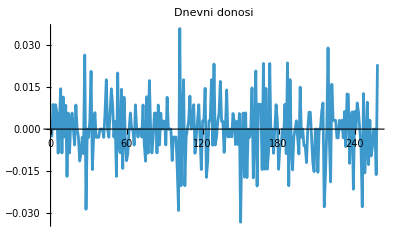

```mathematica
ListLinePlot[donos,PlotLabel->"Dnevni donosi"]
```

Vidimo, da je bil 102. dan v letu najbolj donosen, najmanj pa 150.
Vidimo, da je imela delnica 17.13% letno volatilnost, kar je še zmerno.

```mathematica
volatilnost = StandardDeviation[donos]
```

0.0106449

```mathematica
letnaVolatilnost = volatilnost*Sqrt[Length[donos]]
```

0.170983

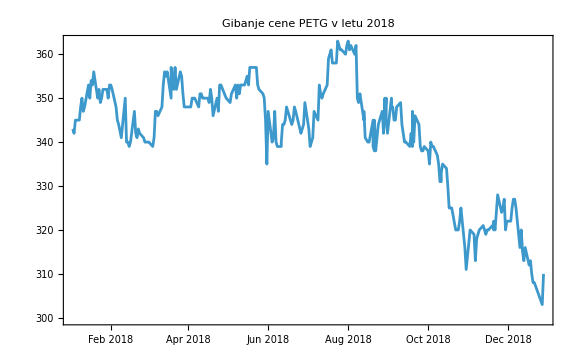

```mathematica
DateListPlot[Transpose[{datumi,cene}],Joined->True,PlotLabel->"Gibanje cene PETG v letu 2018",ImageSize->Large]
```

Graf gibanje delnice v letu 2018.

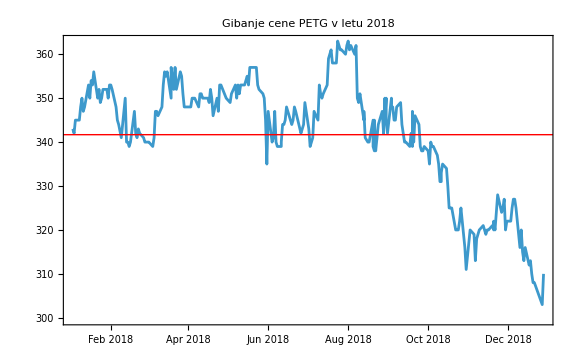

```mathematica
povprecna=Mean[cene];

DateListPlot[Transpose[{datumi,cene}],Joined->True,PlotLabel->"Gibanje cene PETG v letu 2018",ImageSize->Large,Epilog->{{Red,Thick,InfiniteLine[{{Min[datumi],povprecna},{Max[datumi],povprecna}}]}}]
```

Graf gibanja delnice v letu 2018 z rdečo črto pri povprečni vrednosti skozi celo leto.

```mathematica
razlike = Differences[cene];
```

```mathematica
obarvaneCrte=Module[{crte={},n=Length[cene]},Do[If[cene[[i+1]]>cene[[i]],AppendTo[crte,{Green,Line[{{datumiReal[[i]],cene[[i]]},{datumiReal[[i+1]],cene[[i+1]]}}]}],If[cene[[i+1]]<cene[[i]],AppendTo[crte,{Red,Line[{{datumiReal[[i]],cene[[i]]},{datumiReal[[i+1]],cene[[i+1]]}}]}]]],{i,1,n-1}];
crte];
```

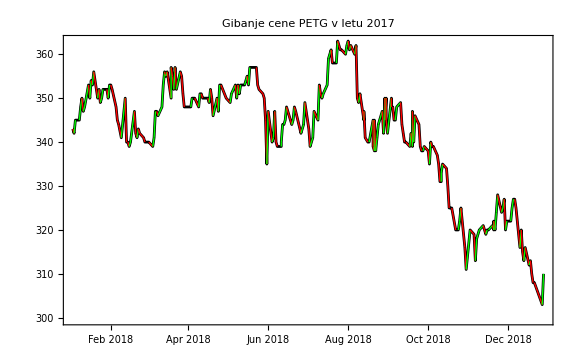

```mathematica
Show[DateListPlot[Transpose[{datumi,cene}],PlotStyle->Black,Joined->True,PlotLabel->"Gibanje cene PETG v letu 2017",ImageSize->Large],Graphics[obarvaneCrte]]
```

Graf delnice z obdobji rasti in padanja.

## Primerjava DAX, SP500 in PETG

Tukaj bom primerjal delnice DAX, SP500 in PETG. Pogledal bom razlike v volatilnost, donosih, ...
Najprej pa vse narišimo na isti graf.

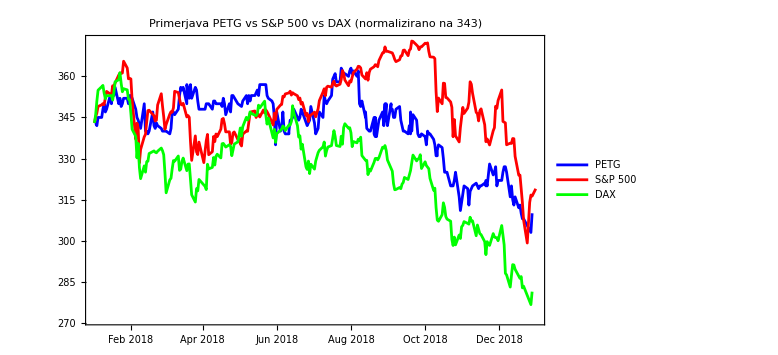

```mathematica
DateListPlot[{petg,sp500norm,daxnorm},Joined->True,PlotStyle->{Blue,Red,Green},PlotLegends->{"PETG","S&P 500","DAX"},ImageSize->Large,PlotLabel->"Primerjava PETG vs S&P 500 vs DAX (normalizirano na 343)"]
```

Vidimo, da so vsi (PETG, S&P 500, DAX) v drugi polovici leta padli. Sicer sta PETG in DAX, ki sta evropska, padla največ, medtem ko je S&P 500, ki je amriški, še nekoliko zdržal padec.
Letni donos vseh treh delnic:

```mathematica
donosi[pairs_]:=Last[pairs[[All,2]]]/First[pairs[[All,2]]]-1;

{"PETG"->NumberForm[100*donosi[petg],{4,1}],"S&P500"->NumberForm[100*donos[sp500norm],{4,1}],"DAX"->NumberForm[100*donosi[daxnorm],{4,1}]}
```

{PETG→-9.6,S&P500→-7.0,DAX→-18.0}

Vidimo, da se je najbolj splašalo kupiti S&P500, najmanj pa DAX.

```mathematica
dnevniDonosi[pairs_]:=Differences[pairs[[All,2]]]/Most[pairs[[All,2]]];
volatilnostf[pairs_]:=StandardDeviation[dnevniDonosi[pairs]]*Sqrt[Length[pairs]];

{"PETG"->volatilnostf[petg],"S&P500"->volatilnostf[sp500norm],"DAX"->volatilnostf[daxnorm]}
```

{PETG→0.171314,S&P500→0.170305,DAX→0.154961}

VIdimo, da je DAX najmanj volatilna in zaradi tega, najmanj tvegana. Najbolj je PETG.

Primerjava gibanja delnice PETG z indeksom S&P 500 in nemškim indeksom DAX v letu 2018 pokaže, da so vse tri naložbe leto zaključile z negativnim donosom. Delnica PETG je izgubila –9,6 % vrednosti, kar je nekoliko več kot padec indeksa S&P 500 (–7,0 %), a manj kot padec nemškega indeksa DAX (–18,0 %). To kaže, da se je PETG gibal podobno kot širši trgi, vendar z nekoliko večjo občutljivostjo, pri čemer je bil padec manj izrazit kot pri DAX-u, a večji kot pri ameriškem trgu.

## Kupec, ki naključno kupuje in prodaja

V tem delu bom simuliral kupca, ki naključno kupuje in prodaja delnice. Na koncu bom dobiček/izgubo od vsake prodaje seštel, da vidimo ali se je v delnico splačalo vlagati.

```mathematica
SeedRandom[1];


nakupi=RandomSample[Range[1,Length[cene]-6],10];

transakcije=Table[Module[{kup=k,prod},prod=Min[kup+RandomInteger[{1,150}], Length[datumi]];
If[prod<=Length[cene],{kup,prod},Nothing]],{k,nakupi}];

rezultati=Table[Module[{kup=t[[1]],prod=t[[2]]},{datumi[[kup]],cene[[kup]],datumi[[prod]],cene[[prod]],cene[[prod]]-cene[[kup]]}],{t,transakcije}];

skupniDobicek=Total[rezultati[[All,5]]];

Grid[Prepend[Append[rezultati,{"Skupaj","","","",skupniDobicek}],{"Datum nakupa","Cena nakupa","Datum prodaje","Cena prodaje","Dobiček"}],Frame->All]
```

Datum nakupa | Cena nakupa | Datum prodaje | Cena prodaje | Dobiček
Thu 18 Oct 2018 | 325. | Wed 14 Nov 2018 | 319. | -6.
Thu 5 Apr 2018 | 350. | Tue 19 Jun 2018 | 344. | -6.
Thu 14 Jun 2018 | 345. | Mon 30 Jul 2018 | 360. | 15.
Mon 15 Jan 2018 | 353. | Wed 6 Jun 2018 | 347. | -6.
Thu 24 May 2018 | 353. | Wed 18 Jul 2018 | 360. | 7.
Fri 6 Apr 2018 | 350. | Thu 26 Jul 2018 | 361. | 11.
Mon 8 Oct 2018 | 337. | Fri 28 Dec 2018 | 310. | -27.
Wed 23 May 2018 | 357. | Fri 25 May 2018 | 352. | -5.
Wed 28 Nov 2018 | 327. | Fri 28 Dec 2018 | 310. | -17.
Fri 16 Feb 2018 | 340. | Tue 19 Jun 2018 | 344. | 4.
Skupaj |  |  |  | -30.

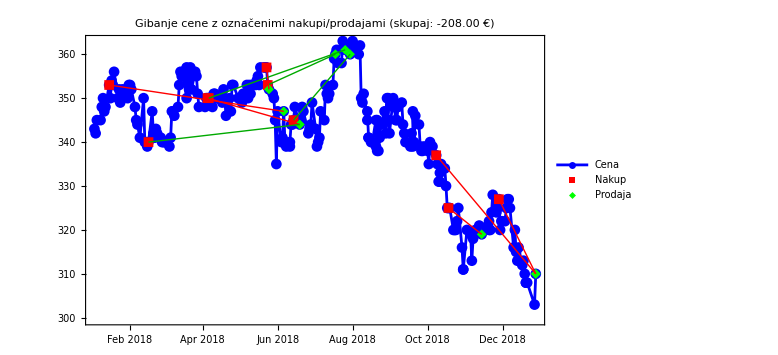

```mathematica
kupIdx=transakcije[[All,1]];
prodIdx=transakcije[[All,2]];

kupTocke=Transpose[{datumi[[kupIdx]],cene[[kupIdx]]}];
prodTocke=Transpose[{datumi[[prodIdx]],cene[[prodIdx]]}];

dobicki=cene[[prodIdx]]-cene[[kupIdx]];
segBarve=If[#>=0,Darker[Green],Red]&/@dobicki;
segCrte=MapThread[{#3,Thick,Line[{{datumi[[#1]],cene[[#1]]},{datumi[[#2]],cene[[#2]]}}]}&,{kupIdx,prodIdx,segBarve}];

DateListPlot[
{Transpose[{datumi,cene}],kupTocke,prodTocke},
Joined->{True,False,False},
PlotStyle->{Blue,Red,Green},
PlotMarkers->{Automatic,{Automatic,10},{Automatic,10}},
PlotLegends->{"Cena","Nakup","Prodaja"},Epilog->segCrte,
ImageSize->Large,
PlotLabel->Row[{"Gibanje cene z označenimi nakupi/prodajami (skupaj: ",
NumberForm[Total[dobički],{6,2}]," €)"}]]
```

## Sklepna analiza

Na podlagi analize delnice PETG v letu 2018 lahko povzamemo naslednje ugotovitve:
1. Osnovne značilnosti gibanja:
	- Najnižja cena delnice je bila 17.13 EUR, najvišja pa okoli 36.6 EUR
	- Povprečna cena je znašala približno 25 EUR
	- V drugi polovici leta se je trend gibanja obrnil navzdol, kar je razvidno iz grafa gibanja cene in preseganja povprečja.
2. Donosi in volatilnost:
	- V letu 2018 je bilo opravljenih 258 trgovalnih dni, od tega je bilo 102 dni pozitivnih donosov in 115 negativnih donosov in 41 jih je bilo enakih 0.
	- Standardni odklon donosov je znašal približno 0,01.
	- Izračunana letna colatilnost je bila okoli 17%, kar nakazuje na zmerno tvegano naložbo.
3. Strategija naključnega kupca:
	- Simulacija je pokazala, da je kupec, ki je naključno kupocal in prodajal delnico skozi leto, ustvaril skupno izgubu 208 EUR.
	- To nakazuje, da je bila strategija naključnih nakupov in prodaj v tem primeru neučinkovita.
4. Tržni trend:
	- Pregled grafa jasno pokaže, da je bila zečetek leta pozitiven, saj je cena naraščala do sredine leta, na to pa je sledil daljši trend padanja, ki se je nadaljvela do konca leta.